```mathematica
?Rule
```

lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs.

```mathematica
?ReplaceAll
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
list ={1, 2,3 , 4, 5, 6}
```

{1,2,3,4,5,6}

```mathematica
list /.1->x
```

{10.,20.,30.,40.,50.,60.}→x

```mathematica
x
```

x

```mathematica
?MatchQ
```

MatchQ[expr,form] returns True if the pattern form matches expr, and returns False otherwise.
MatchQ[form] represents an operator form of MatchQ that can be applied to an expression.

```mathematica
MatchQ[1, _Interger]
```

False

```mathematica
?Blank
```

_ or Blank[] is a pattern object that can stand for any Wolfram Language expression. 
_h or Blank[h] can stand for any expression with head h.

```mathematica
?Rule
```

lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs.

```mathematica
?ReplaceAll
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
list = {1, 2, 3, 1, 2, 3}
```

{1,2,3,1,2,3}

```mathematica
ReplaceAll[list, 1->x]
```

{x,2,3,x,2,3}

```mathematica
list /. 1 ->x
```

{x,2,3,x,2,3}

```mathematica
list /. {1->x, 2->y}
```

{x,y,3,x,y,3}

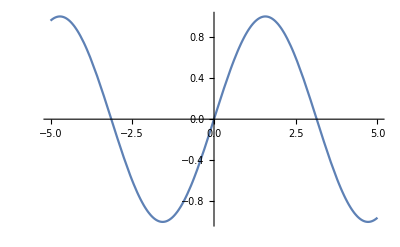
{x,y,-Graphics-,x,y,-Graphics-}

```mathematica
list /. {1->x, 2->y, 3->Plot[Sin[x], {x, -5, 5}, ImageSize->Tiny]}
```

```mathematica
Sin[x] /. Sin->Cos
```

Cos[x]

```mathematica
Sin[x]+y /. Sin[x]->z^2
```

y+z^2

```mathematica
nestdList = {1, {{{4}}}, 5}
```

{1,{{{4}}},5}

```mathematica
nestdList = nestdList /. {4} ->4
```

{1,{{4}},5}

```mathematica
nestdList = nestdList /. {4} ->4
```

{1,{4},5}

```mathematica
nestdList = nestdList /. {4} ->4
```

{1,4,5}

```mathematica
nestdList = nestdList /. {4} ->4
```

{1,4,5}

```mathematica
f[x] /. x->f[x]
```

f[f[x]]

```mathematica
?MatchQ
```

MatchQ[expr,form] returns True if the pattern form matches expr, and returns False otherwise.
MatchQ[form] represents an operator form of MatchQ that can be applied to an expression.

```mathematica
MatchQ[1, _Integer]
```

True

```mathematica
?Blank
```

_ or Blank[] is a pattern object that can stand for any Wolfram Language expression. 
_h or Blank[h] can stand for any expression with head h.

```mathematica
Head[2]
```

Integer

```mathematica
Head[1.1]
```

Real

```mathematica
list /. {x_Integer->Sin[x]}
```

{Sin[1],Sin[2],Sin[3],Sin[1],Sin[2],Sin[3]}

```mathematica
FullForm[x_Integer]
```

Pattern[x,Blank[Integer]]

```mathematica
?Pattern
```

s:obj represents the pattern object obj, assigned the name s.

```mathematica
x:Blank[Integer]
```

x_Integer

```mathematica
List /. {x:_Integer->Sin[x]}
```

List

```mathematica
?RandomInteger
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.

```mathematica
list = Join[RandomInteger[100, 2], {1, 2, 3}, RandomInteger[100, 2]]
```

{42,18,1,2,3,25,68}

```mathematica
list /. {a_, b_, 1, 2, 3, c_, d_}->{a, b, "hello", c, d}
```

{42,18,hello,25,68}

```mathematica
?BlankSequence
```

__ (two _ characters) or BlankSequence[] is a pattern object that can stand for any sequence of one or more Wolfram Language expressions. 
__h or BlankSequence[h] can stand for any sequence of one or more expressions, all of which have head h.

```mathematica
list /. {a__, b__, 1, 2, 3, c__, d__}->{a, b, "hello", c, d}
```

{42,18,hello,25,68}

```mathematica
a
```

a

```mathematica
Framed[x, Background->Yellow]
```

x

```mathematica
?PatternTest
```

p?test is a pattern object that stands for any expression that matches p, and on which the application of test gives True.

```mathematica
?Negative
```

Negative[x] gives True if x is a negative number.

```mathematica
Negative[-100]
```

True

```mathematica
list /. {n_?Positive->Framed[n, Background->Yellow]}
```

{42,18,1,2,3,25,68}

```mathematica
list /. {n_?EvenQ->Framed[n, Background->Yellow]}
```

{42,18,1,2,3,25,68}

```mathematica
list /. {n_Integer?EvenQ->Framed[n, Background->Yellow]}
```

{42,18,1,2,3,25,68}

```mathematica
?Condition
```

patt/;test is a pattern which matches only if the evaluation of test yields True. 
lhs:>rhs/;test represents a rule which applies only if the evaluation of test yields True. 
lhs:=rhs/;test is a definition to be used only if test yields True.

```mathematica
list /. {n_ /; EvenQ[n]->Framed[n, Background->Yellow]}
```

{42,18,1,2,3,25,68}

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

```mathematica
Cases[Range[20], _?EvenQ]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
?Set
```

lhs=rhs evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
{l_1,l_2,…}={r_1,r_2,…} evaluates the r_i, and assigns the results to be the values of the corresponding l_i.

```mathematica
?Rule
```

lhs->rhs or lhs→rhs represents a rule that transforms lhs to rhs.

```mathematica
?SetDelayed
```

lhs:=rhs assigns rhs to be the delayed value of lhs. rhs is maintained in an unevaluated form. When lhs appears, it is replaced by rhs, evaluated afresh each time.

```mathematica
?RuleDelayed
```

lhs:>rhs or lhs:>rhs represents a rule that transforms lhs to rhs, evaluating rhs only after the rule is used.

```mathematica
rand2 := RandomInteger[100]
```

```mathematica
rand2
```

62

```mathematica
lhs = Table[x, {10}]
```

{x,x,x,x,x,x,x,x,x,x}

```mathematica
lhs /. x->RandomInteger[100]
```

{84,84,84,84,84,84,84,84,84,84}